-Graphics-

Bienvenidos a mmAeScience!
https://github.com/josemramirez/mmaescience/calc_intro -[for MMaTeX]_beta^v14

# eScience - Funciones Elementales

◀ prev - + prox ▶

e Guardar
d Resetear

### Visión general

```mathematica
Hasta ahora, ha creado funciones para expresar cómo cambia una cantidad con respecto a otras. Sin embargo, hay tantos tipos diferentes de funciones que uno puede perderse entre todas ellas.
```

Aquí hay un gráfico de varias funciones:

```mathematica
f[x_] := x + 2;
```

```mathematica
g[x_] := 6 x^3  - x - 3;
```

```mathematica
h[x_] := 3^x ;
```

```mathematica
r[x_] := 15 Log[x];
```

```mathematica
s[x_] := 10 Sin[x];
```

```mathematica
t[x_] :=2/(x^2)
```

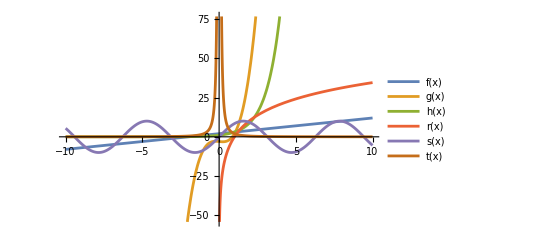

```mathematica
Plot[{f[x], g[x], h[x], r[x], s[x], t[x]}, {x, -10, 10}, PlotLegends -> Expressions]
```

¿Qué se puede suponer sobre estas funciones basándose únicamente en sus gráficos?

```mathematica
Esta lección categoriza muchos de los tipos de funciones que encontrará más adelante en el curso.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Lineal

Considere la siguiente función:

```mathematica
f[x_] := x + 3
```

Si lo trazas, puedes ver que forma una línea:

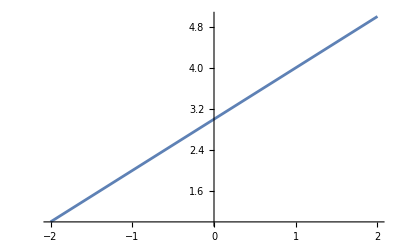

```mathematica
Plot[f[x], {x, -2, 2}]
```

La función general f[x]=m x+b se denomina función lineal y tiene pendiente m e intersección con el eje y b. La función cruza el eje y en b y aumenta a una tasa constante de m unidades por cada aumento de 1 unidad de x.

◀ prev - + prox ▶

e Guardar
d Resetear

### Polinomios

```mathematica
La siguiente función se conoce como polinomio:
```

```mathematica
f[x_]:= 3 x^4  - x^2  + 7 x + 6
```

Aquí esta su gráfica:

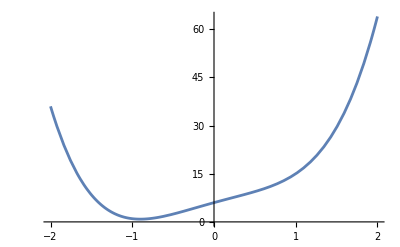

```mathematica
Plot[f[x], {x, -2, 2}]
```

```mathematica
Los polinomios generalmente tienen la forma f[x]=Subscript[a, n] x^n+Subscript[a, n-1] x^(n-1)+...+Subscript[a, 1] x+Subscript[a, 0], donde n no es negativo y las constantes Subíndice[a, n],...,Subíndice[a, 0] se denominan sus coeficientes.
```

```mathematica
Si Subíndice[a, n]≠0, entonces el grado del polinomio es n.
```

```mathematica
La función mostrada tiene grado 4.
```

```mathematica
Las funciones lineales tienen grado 1.
```

```mathematica
Una función con grado 2 se denomina función cuadrática.
```

Una función de grado 3 se denomina función cúbica.

◀ prev - + prox ▶

e Guardar
d Resetear

### Funciones de potencia

Una función de potencia es una función de la forma f[x]=x^a, donde a es una constante. Las funciones de potencia pueden adoptar varias formas. Cuando a es un entero positivo, el resultado son polinomios.

```mathematica
Estos polinomios tienen patrones especiales, como se ve en el siguiente gráfico:
```

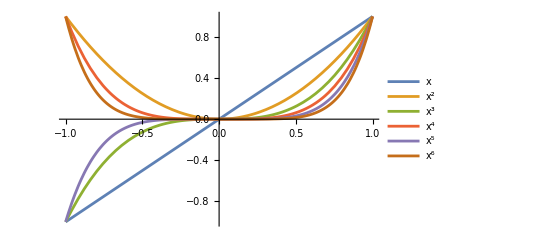

```mathematica
Plot[{x, x^2 , x^3 , x^4 , x^5 , x ^6}, {x, -1, 1},
 PlotLegends -> Expressions]
```

```mathematica
Las funciones de grado impares son impares y las funciones de grado par son pares.
```

Cuando a=1/n para n un entero positivo, el resultado son funciones raíz. Por ejemplo, la función de raíz cuadrada f[x]=Sqrt[x] es una función de raíz, con exponente 1/2.

Las funciones raíz también tienen patrones especiales, como se ve en este gráfico:

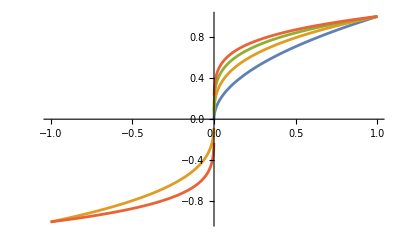

```mathematica
Plot[{x^(1/2), Surd[x, 3], x^(1/4), Surd[x, 5]}, {x, -1, 1}, PlotLegends -> Expressions]
```

Para n impar, la función se define en todas partes. Para n even, la función solo se define en [0,∞).

◀ prev - + prox ▶

e Guardar
d Resetear

### Racional

```mathematica
Sean P[x] y Q[x] dos polinomios. Una función racional f es un cociente de los polinomios P y Q. En otras palabras, f[x]=P[x]/Q[x]. Cuando Q es constante, el resultado son los polinomios como antes.
```

```mathematica
La función recíproca f[x]=x^-1=1/x es una función racional.
```

Aquí está su gráfico:

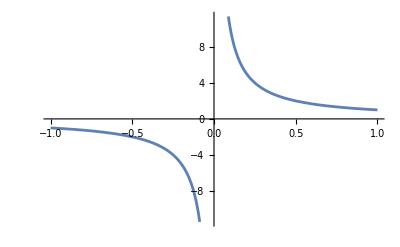

```mathematica
1
Plot[-, {x, -1, 1}]
                  x
```

Observe cómo el gráfico no parece tomar un valor en x=0. Esto se debe a que la función no está definida allí.

```mathematica
La función se evalúa como 1/0, que no está definido para los números reales. En general, las funciones racionales se definen en todas partes, excepto cuando sus denominadores son 0.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Algebraico

```mathematica
Todas las funciones cubiertas hasta ahora se denominan funciones algebraicas. Esto se debe a que se pueden hacer sumando, restando, multiplicando, dividiendo o tomando raíces de funciones polinómicas y otras funciones algebraicas.
```

La siguiente función es una función algebraica:

```mathematica
3
                      Sqrt[x + Sqrt[3 x  + 1]]
f[x_] := ------------------------]
                                      2
                            CubeRoot[x
```

```mathematica
Aquí está su gráfico:
```

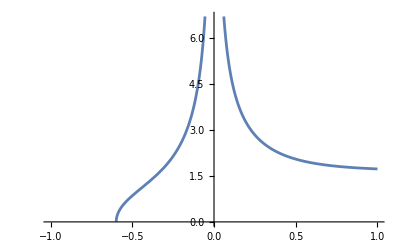

```mathematica
Plot[f[x], {x, -1, 1}]
```

```mathematica
Las funciones algebraicas vienen en una variedad de formas.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Trigonométrico

Las funciones seno, coseno y tangente son funciones trigonométricas y no algebraicas. Se pueden definir en función de las proporciones de los lados de un triángulo, pero las funciones generales van más allá. Al introducir valores en funciones trigonométricas en Wolfram Language, se asume que se utiliza la medida de radianes.

Así que Sin[30]≠1/2, pero Sin[π/6]=1/2. Para que se evalúe como grados, agregue Grado al final:

```mathematica
Pi
{Sin[30], Sin[--], Sin[30 Degree]}
                           6
```

{Sin[30],1/2,1/2}

Aquí están las gráficas de las tres funciones trigonométricas seno, coseno y tangente en el rango [-2π,2π]:

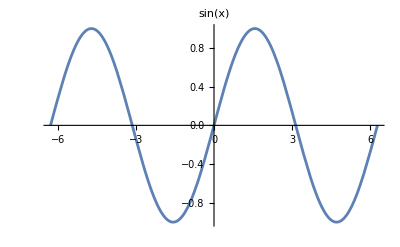
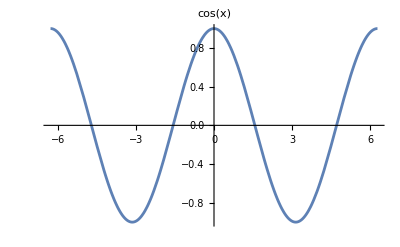
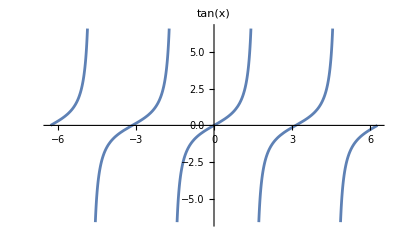

```mathematica
Table[Plot[i, {x, -2 Pi, 2 Pi}, PlotLabel -> i], {i, {Sin[x], Cos[x], Tan[x]}}]
```

Nótese que cada función trigonométrica es muy repetitiva; Toman el mismo valor cada intervalo de 2π.

Cuando una función f tiene la propiedad f[x+t]=f[x] para todo x, es periódica con el período t.

El seno y el coseno tienen un período 2π.

```mathematica
La tangente tiene período π.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Trigonométrico recíproco

```mathematica
Los recíprocos de seno, coseno y tangente son cosecante, secante y cotangente, respectivamente. En otras palabras, Cosecante = 1 / Seno , Secante = 1 / Coseno y Cotangente = 1 / Tangente.
```

Secante, cosecante y cotangente también son funciones trigonométricas. Aquí están sus gráficos y recíprocos en el rango [-2π,2π]:

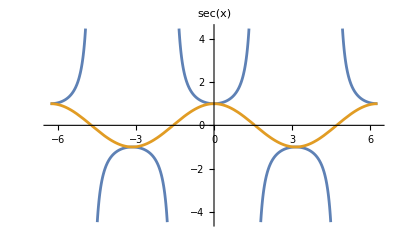
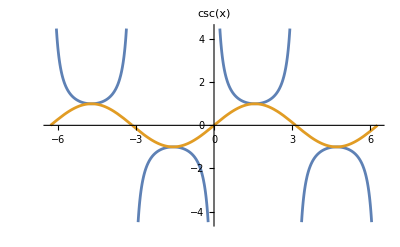
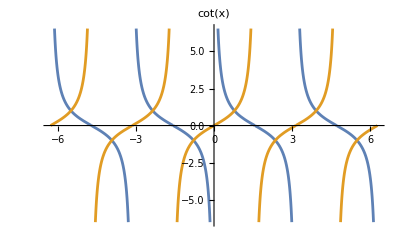

```mathematica
1
Table[Plot[{i, -}, {x, -2 Pi, 2 Pi}, PlotLabel -> i], {i, {Sec[x], Csc[x], Cot[x]}}]
                            i
```

```mathematica
Observe que secante, cosecante y cotangente (en rojo) tienen varios lugares donde no están definidos. Estos lugares corresponden a lugares donde sus recíprocos coseno, seno y tangente (en azul) son 0.
```

```mathematica
La secante y la cosecante tienen un período 2π.
```

La cotangente tiene período π.

◀ prev - + prox ▶

e Guardar
d Resetear

### Exponencial

Mientras que las funciones de potencia tienen la forma x^a, las funciones exponenciales tienen la forma a^x. Cuando a>1, hay una función de crecimiento exponencial.

```mathematica
Aquí hay un gráfico de la función de crecimiento exponencial f[x]=2^x:
```

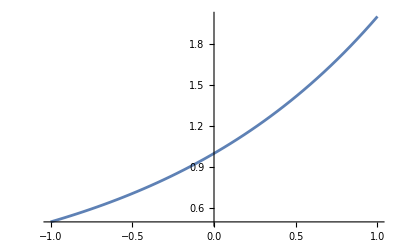

```mathematica
x
Plot[2 , {x, -1, 1}]
```

Cuando 0<a<1, hay una función de decaimiento exponencial.

```mathematica
Aquí hay un gráfico de la función de decaimiento exponencial g[x]=0.5^x:
```

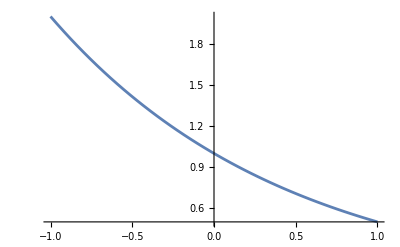

```mathematica
x
Plot[0.5 , {x, -1, 1}]
```

```mathematica
Todas las funciones exponenciales de la forma a^x pasan el eje y en el punto (0,1), porque a^0=1 para cualquier número a.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Logarítmico

```mathematica
Las funciones logarítmicas tienen la forma f[x]=Subíndice[log, a]x y se pueden definir como las inversas de las funciones exponenciales. Así que a^f[x]=x. Aquí a se conoce como la base.
```

Aquí se asume que siempre que se omite la base en la expresión Subíndice[Log, a]x, la base es el número natural e~2.718.

Wolfram Language representa funciones logarítmicas con la función Log.

Aquí está la gráfica de la función logarítmica con base e (y un esquema general para base mayor que 1):

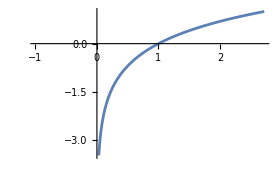

```mathematica
Plot[Log[x], {x, -1, E}]
```

```mathematica
Observe que el dominio es todo números reales positivos (es decir, (0,∞)). Log[e]=1 ya que e^1=e.
```

Aquí está la gráfica de la función logarítmica con base 1/4 (y un esquema general para la base entre 0 y 1):

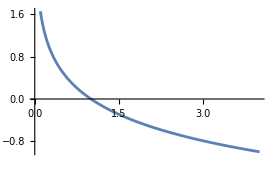

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
1
Plot[Log[-, x], {x, 0, 4}]
                      4
```

### Resumen

Las funciones tienen muchas formas diferentes y pueden tener una variedad de gráficos.

Las funciones lineales tienen gráficos que parecen líneas.

```mathematica
Las funciones polinómicas incluyen funciones lineales y tienen todos los números reales como su dominio.
```

```mathematica
La función de potencia tiene sus entradas llevadas a una potencia constante.
```

Las funciones racionales incluyen funciones polinómicas y se definen cuando sus denominadores no son 0.

Las funciones algebraicas incluyen funciones racionales y se crean sumando, restando, multiplicando, dividiendo y echando raíces.

```mathematica
Las funciones trigonométricas tienen su base en la geometría y son periódicas.
```

Las funciones exponenciales y sus inversas, las funciones logarítmicas, tienen base positiva a y pueden crecer o decaer.

La siguiente lección cubrirá los límites, el punto de partida de cualquier curso de iniciación en el cálculo.

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 1: Propiedades de una línea

Una recta pasa por los puntos (4,1) y (−3,7). Halla su pendiente y su intersección con el eje y, y traza la función en el rango [-5,5].

#### Solución

```mathematica
Dado que hay una recta, su función debe ser lineal y tener la forma f[x]=m x+b, donde m es la pendiente y b es la intersección con el eje y.
```

La pendiente se puede calcular dividiendo el cambio en y por el cambio en x para los dos puntos:

```mathematica
7 - 1
m = ------
                 -3 - 4
```

-6/7

Ahora reemplaza uno de los puntos en la función para hallar b:

```mathematica
Solve[1 == m 4 + b, b]
```

{{b→31/7}}

```mathematica
Dado que la función tiene la ecuación f[x]=-6/7 x+31/7, aquí está la gráfica de la función con los dos puntos:
```

```mathematica
x   31
f[x_] := -6 - + --
                         7   7
```

La gráfica en el rango [-5,5] es:

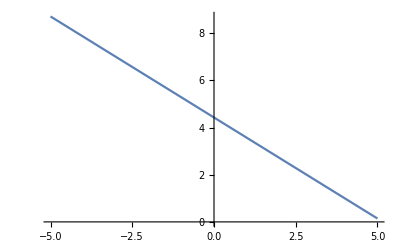

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, -5, 5}]
```

### Ejercicio 2: Polinomios

Un polinomio tiene grado 6 y tiene coeficientes Subíndice[a, 6]=2, Subíndice[a, 5]=6, Subíndice[a, 4]=0, Subíndice[a, 3]=1, Subíndice[a, 2]=−7, Subíndice[a, 1]=3 y Subíndice[a, 0]=14. Traza el polinomio en una gráfica. ¿Cuál es su valor cuando se introduce el número 45?

#### Solución

Según la información dada, el polinomio tiene la forma 2x^6+6x^5+x^3-7x^2+3x+14.

```mathematica
Conviértelo en una función:
```

```mathematica
6      5    3      2
f[x_] := 2 x  + 6 x  + x  - 7 x  + 3 x + 14
```

Grafique el polinomio:

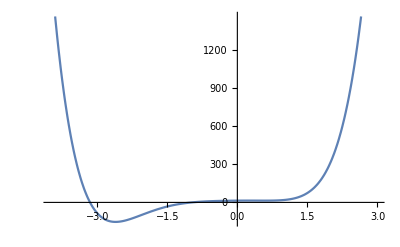

```mathematica
Plot[f[x], {x, -4, 3}]
```

Evalúe la función en 45:

```mathematica
f[45]
```

17714777099

```mathematica
La función (y el polinomio) tiene el valor 17.714.777.099 cuando x=45.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 3: Racional

Grafique la siguiente función racional para encontrar su dominio:

```mathematica
3
                                 x  + 6 x - 7
f[x_] := -----------------------------------
                          4      3        2
                      20 x  + 4 x  - 359 x  - 130 x + 888
```

#### Solución

```mathematica
Aquí está el gráfico de la función en el rango [-5,5]:
```

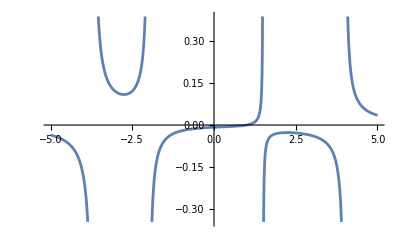

```mathematica
Plot[f[x], {x, -5, 5}]
```

Para encontrar el dominio de la función, establece su denominador en 0 y resuelve x:

```mathematica
4      3        2
Solve[20 x  + 4 x  - 359 x  - 130 x + 888 == 0, x]
```

{{x→-37/10},{x→-2},{x→3/2},{x→4}}

```mathematica
La función tiene dominio (-∞,-3.7)∪(-3.7,-2)∪(-2,1.5)∪(1.5,4)∪(4,∞).
```

También podría haberlo calculado con FunctionDomain:

```mathematica
FunctionDomain[f[x], x]
```

x<-37/10||-37/10<x<-2||-2<x<3/2||3/2<x<4||x>4

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 4: Planeta Aurora

```mathematica
El planeta ficticio Aurora tarda 501 días en girar alrededor de su estrella. El número de horas de luz diurna se puede modelar mediante la siguiente función:
```

```mathematica
Pi
daylight[t_] := 15 + 4.7 Cos[2 --- (t - 240)]
                                            501
```

```mathematica
donde t es el número de días después de su año nuevo. Grafique la función y encuentre cuánto dura un día en el día 397^ del año aurorano.
```

#### Solución

La función de luz diurna se traza con Plot:

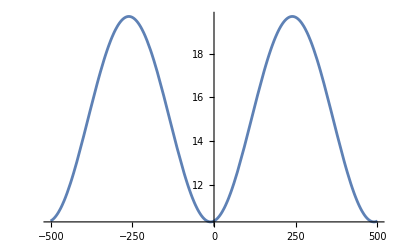

```mathematica
Plot[daylight[t], {t, -501, 501}]
```

```mathematica
Conecte el 397 a la función:
```

```mathematica
daylight[397]
```

13.1776

El día 397^ del año, el día aurorano dura unas 13,18 horas (o 13 horas, 10 minutos y unos 36 segundos).

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 5: Colonia de bacterias

Una colonia de bacterias crece de acuerdo con el siguiente modelo de crecimiento exponencial, donde t está en horas:

```mathematica
t
bacterialgrowth[t_] := 1.97
```

Si la colonia se vuelve demasiado grande (por ejemplo, alcanza una cantidad M), se usan antibióticos para hacer que la colonia muera de acuerdo con el siguiente modelo de descomposición exponencial, donde t está en horas:

```mathematica
t
bacterialdecay[m_, t_] := m 0.67
```

```mathematica
Si se permite que la colonia de bacterias crezca durante 30 horas y luego es atacada por antibióticos, ¿cuánto tiempo tardará la colonia en contener solo 1000 miembros?
```

#### Solución

Primero, evalúe el tamaño de la colonia a las 30 horas:

```mathematica
bacterialgrowth[30]
```

6.82318×10^8

Luego, reemplaza este número en la función de decaimiento exponencial y resuelve t cuando la función sea igual a 1000:

```mathematica
Quiet[Solve[1000 == bacterialdecay[bacterialgrowth[30], t], t]]
```

{{t→33.5431}}

```mathematica
Se necesitarán unas 33.542 horas (o 33 horas, 32 minutos y unos 36 segundos) para reducir la población bacteriana a 1000.
```

```mathematica
Aquí están los dos gráficos juntos:
```

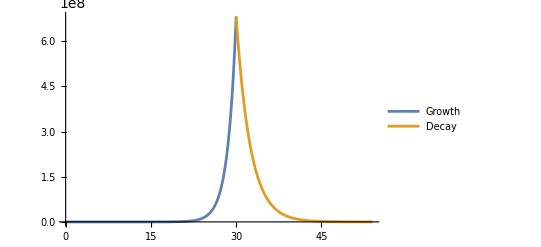

```mathematica
Plot[{Piecewise[{{bacterialgrowth[t], 0 <= t <= 30}}, Null], Piecewise[{{bacterialdecay[bacterialgrowth[30], t - 30], 30 <= t <= 54}}, Null]}, {t, 0, 54}, PlotRange -> All, PlotLegends -> {Growth, Decay}]
```

## Referencias

https : // www . wolfram - media . com/products/introduction - to - calculus/

```mathematica
mmAeScienceDB1="mmAeScienceDB1_v1.mx";
DumpSave[$WorkDir<>"mmAeScienceDB/"<>mmAeScienceDB1,"Global`"];
```

```mathematica
buttons=Row[{
Column[{
Button["e Guardar",(NotebookFind[EvaluationNotebook[],#,All,CellTags];SelectionEvaluate[EvaluationNotebook[]])&/@{"mmAeSRunSave"};],
Button["d Resetear",(NotebookFind[EvaluationNotebook[],#,All,CellTags];SelectionEvaluate[EvaluationNotebook[]])&/@{"mmAeSRunCollapse"};]
}]
}]
```

e Guardar
d Resetear